```mathematica
(* Define constants *)
```

```mathematica
hp:=6.62607004×10^(-34)     (* Planck constant, in J s *)
```

```mathematica
hbar:=hp/(2 Pi)    (* hbar *)
```

```mathematica
kb:=1.38064852×10^(-23)    (* Boltzmann constant, in J/K *)
```

```mathematica
ec:=1.60217662×10^(-19)     (* elementary charge, in coulombs C *)
```

```mathematica
phi0 := hp/(2 ec)    (* magnetic flux quantum, in Js/C = J/A *)
```

```mathematica
vcpw:=1.2 10^8     (* propagation velocity in CPW, in m/s, (fig4) *)
```

```mathematica
z0 :=55      (* impedance of CPW, in ohms (fig4) *)
```

```mathematica
ic:=1.25 10^(-6)    (* critical current of Josephson junctions, in A (fig4) *)
```

```mathematica
ej=ic phi0/(2 Pi)   (* Josephson energy of SQUID junctions, in J (fig4) *)
```

4.11382×10^-22

```mathematica
ej0:=1.3 ej    (* Josephson energy for static applied magnetic flux (6) *)
```

```mathematica
dej:=ej0/4     (* amplitude of tunable Josephson energy for weak harmonic drive (fig4) *)
```

```mathematica
l0=z0/vcpw    (* inductance of CPW per unit length, in henry/m = V s/(A m) *)
```

4.58333×10^-7

```mathematica
l0eff=(phi0/(2Pi))^2/(ej0 l0)   (* effective length, in m (fig4) *)
```

0.000441877

```mathematica
dleff=l0eff/4     (* effective length modulation, in m (fig4) *)
```

0.000110469

```mathematica
omega:=2Pi * 18.6 10^9     (* drive frequency, in rad/s; note: omega = 2 Pi f *)
```

```mathematica
(* Numerical calculation for periodic array, see notes TR and CM *)
```

```mathematica
g[n_,m_]:=KroneckerDelta[n,m]+(0.5dej/ej0) Sqrt[Abs[ww[m]/ww[n]]](KroneckerDelta[n,m+1]+KroneckerDelta[n,m-1])
```

```mathematica
ww[n_]:=k omega/nd +(nomega+1-n) omega
```

```mathematica
bigg[m_,n_]:=1/2   I  vcpw/(ww[m]l0eff)  g[n,m]     (* note order of indices *)
```

```mathematica
one[m_,n_] :=KroneckerDelta[m,n]       (* unity matrix *)
```

```mathematica
biggmatrix:=Table[bigg[m,n],{m,1,2nomega+1},{n,1,2nomega+1}]
```

```mathematica
onematrix:=Table[one[m,n],{m,1,2nomega+1},{n,1,2nomega+1}]
```

```mathematica
nomega:=1        (* one sideband *)
```

```mathematica
(* test block matrix *)
```

```mathematica
aa:={{1,2},{3,4}}
```

```mathematica
bb:={{5,6},{7,8}}
```

```mathematica
cc:={{9,10},{11,12}}
```

```mathematica
dd:={{13,14},{15,16}}
```

```mathematica
block:=ArrayFlatten[{{aa,bb},{cc,dd}}]
```

```mathematica
MatrixForm[block]
```

(1 | 2 | 5 | 6
3 | 4 | 7 | 8
9 | 10 | 13 | 14
11 | 12 | 15 | 16)

```mathematica
(* end test block matrix *)
```

```mathematica
nd:=10
```

```mathematica
k:=5
```

```mathematica
(* CM, page 4 *)
```

```mathematica
shat:=ArrayFlatten[{{onematrix-biggmatrix,-biggmatrix},{biggmatrix, onematrix+biggmatrix}}]
```

```mathematica
MatrixForm[shat]
```

(1.-0.77458 ⅈ | 0.-0.167701 ⅈ | 0.+0. ⅈ | 0.-0.77458 ⅈ | 0.-0.167701 ⅈ | 0.+0. ⅈ
0.-0.167701 ⅈ | 1.-2.32374 ⅈ | 0.-0.290467 ⅈ | 0.-0.167701 ⅈ | 0.-2.32374 ⅈ | 0.-0.290467 ⅈ
0.+0. ⅈ | 0.+0.290467 ⅈ | 1.+2.32374 ⅈ | 0.+0. ⅈ | 0.+0.290467 ⅈ | 0.+2.32374 ⅈ
0.+0.77458 ⅈ | 0.+0.167701 ⅈ | 0.+0. ⅈ | 1.+0.77458 ⅈ | 0.+0.167701 ⅈ | 0.+0. ⅈ
0.+0.167701 ⅈ | 0.+2.32374 ⅈ | 0.+0.290467 ⅈ | 0.+0.167701 ⅈ | 1.+2.32374 ⅈ | 0.+0.290467 ⅈ
0.+0. ⅈ | 0.-0.290467 ⅈ | 0.-2.32374 ⅈ | 0.+0. ⅈ | 0.-0.290467 ⅈ | 1.-2.32374 ⅈ)

```mathematica
lambdaomega=2Pi vcpw/ omega    (* wavelength associated with drive frequency Omega, in m *)
```

0.00645161

```mathematica
ell:=0.96*lambdaomega      (* lattice constant; with this choice of ell, both the main band *)
(* and the side band are in allowed energy band for omega in [0.48, 0.52] Omega *)
```

```mathematica
p[n_,m_]:=Exp[I (ww[n]/vcpw) ell]  KroneckerDelta[n,m]    (* matrix P, TR page 5 *)
```

```mathematica
nomega:=1   (* one sideband)
```

```mathematica
nd:=10     (* # omega points in (0,Omega) *)
```

```mathematica
k:=5.0
```

```mathematica
pmatrix:=Table[p[m,n],{m,1,2nomega+1},{n,1,2nomega+1}]
```

```mathematica
MatrixForm[pmatrix]
```

(-0.929776+0.368125 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | -0.992115+0.125333 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | -0.992115-0.125333 ⅈ)

```mathematica
phat:=ArrayFlatten[{{pmatrix,0},{0,Conjugate[pmatrix]}}]    (* TR, page 6 *)
```

```mathematica
MatrixForm[phat]
```

(-0.929776+0.368125 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0 | 0 | 0
0.+0. ⅈ | -0.992115+0.125333 ⅈ | 0.+0. ⅈ | 0 | 0 | 0
0.+0. ⅈ | 0.+0. ⅈ | -0.992115-0.125333 ⅈ | 0 | 0 | 0
0 | 0 | 0 | -0.929776-0.368125 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0.+0. ⅈ | -0.992115-0.125333 ⅈ | 0.+0. ⅈ
0 | 0 | 0 | 0.+0. ⅈ | 0.+0. ⅈ | -0.992115+0.125333 ⅈ)

```mathematica
that:=phat.shat      (* transfer matrix *)
```

```mathematica
MatrixForm[that]
```

(-0.644635+1.08831 ⅈ | 0.061735+0.155925 ⅈ | 0.+0. ⅈ | 0.285142+0.720186 ⅈ | 0.061735+0.155925 ⅈ | 0.+0. ⅈ
0.0210186+0.166379 ⅈ | -0.700873+2.43075 ⅈ | 0.0364052+0.288177 ⅈ | 0.0210186+0.166379 ⅈ | 0.291242+2.30542 ⅈ | 0.0364052+0.288177 ⅈ
0.+0. ⅈ | 0.0364052-0.288177 ⅈ | -0.700873-2.43075 ⅈ | 0.+0. ⅈ | 0.0364052-0.288177 ⅈ | 0.291242-2.30542 ⅈ
0.285142-0.720186 ⅈ | 0.061735-0.155925 ⅈ | 0.+0. ⅈ | -0.644635-1.08831 ⅈ | 0.061735-0.155925 ⅈ | 0.+0. ⅈ
0.0210186-0.166379 ⅈ | 0.291242-2.30542 ⅈ | 0.0364052-0.288177 ⅈ | 0.0210186-0.166379 ⅈ | -0.700873-2.43075 ⅈ | 0.0364052-0.288177 ⅈ
0.+0. ⅈ | 0.0364052+0.288177 ⅈ | 0.291242+2.30542 ⅈ | 0.+0. ⅈ | 0.0364052+0.288177 ⅈ | -0.700873+2.43075 ⅈ)

```mathematica
Det[that]    (* det(that)=1 even with drive *)
```

1.-1.22125×10^-15 ⅈ

```mathematica
eigen=Eigenvalues[that]
```

{-0.678802+0.734322 ⅈ,-0.623218+0.782048 ⅈ,-0.744361+0.667778 ⅈ,-0.623218-0.782048 ⅈ,-0.678802-0.734322 ⅈ,-0.744361-0.667778 ⅈ}

```mathematica
Table[Abs[eigen[[n]]],{n,6}]
```

{1.,1.,1.,1.,1.,1.}

```mathematica
(* both main band and side band are in allowed energy band => magnitude of all eigenvalues of that is =1 *)
```

```mathematica
nrepeat :=100     (* number of repeated units *)
```

```mathematica
chat := shat.MatrixPower[that,nrepeat]      (* TR, page 7 *)
```

```mathematica
Det[chat]             (* det(chat) is still =1 *)
```

1.+2.03171×10^-14 ⅈ

```mathematica
eigenchat=Eigenvalues[chat]
```

{0.419943-0.907551 ⅈ,-0.371833+0.9283 ⅈ,-0.371833-0.9283 ⅈ,0.419943+0.907551 ⅈ,-0.658144+0.752892 ⅈ,-0.658144-0.752892 ⅈ}

```mathematica
Table[Abs[eigenchat[[n]]],{n,1,6}]
```

{1.,1.,1.,1.,1.,1.}

```mathematica
MatrixForm[chat]
```

(-0.367855-0.828326 ⅈ | -0.348972-0.395616 ⅈ | -0.189677+0.756584 ⅈ | 2.77556×10^-17-0.458777 ⅈ | -0.186036-0.282145 ⅈ | -0.401723+0.81974 ⅈ
-0.348972-0.395616 ⅈ | -0.291812+0.553091 ⅈ | 9.49241×10^-15-2.6891 ⅈ | 0.186036-0.282145 ⅈ | -2.52021×10^-14+0.538299 ⅈ | 0.223249-2.81354 ⅈ
0.189677-0.756584 ⅈ | -1.24345×10^-14+2.6891 ⅈ | 0.0496329+0.886599 ⅈ | -0.401723-0.81974 ⅈ | 0.223249+2.81354 ⅈ | 4.37428×10^-14+0.864928 ⅈ
-4.4964×10^-15+0.458777 ⅈ | -0.186036+0.282145 ⅈ | -0.401723-0.81974 ⅈ | -0.367855+0.828326 ⅈ | -0.348972+0.395616 ⅈ | -0.189677-0.756584 ⅈ
0.186036+0.282145 ⅈ | 2.39808×10^-14-0.538299 ⅈ | 0.223249+2.81354 ⅈ | -0.348972+0.395616 ⅈ | -0.291812-0.553091 ⅈ | -4.02456×10^-15+2.6891 ⅈ
-0.401723+0.81974 ⅈ | 0.223249-2.81354 ⅈ | -4.39648×10^-14-0.864928 ⅈ | 0.189677+0.756584 ⅈ | 1.59872×10^-14-2.6891 ⅈ | 0.0496329-0.886599 ⅈ)

```mathematica
(* submatrices a, b, c, d of matrix chat, CM page 1 *)
```

```mathematica
asub:=Take[chat,{1,2nomega+1},{1,2nomega+1}]
```

```mathematica
bsub:=Take[chat,{1,2nomega+1},{2nomega+2,2*(2nomega+1)}]
```

```mathematica
csub:=Take[chat,{2nomega+2,2*(2nomega+1)},{1,2nomega+1}]
```

```mathematica
dsub:=Take[chat,{2nomega+2,2*(2nomega+1)},{2nomega+2,2*(2nomega+1)}]
```

```mathematica
(* matrices A, B, C, D, CM page 1 *)
```

```mathematica
Clear[aa,bb,cc,dd]
```

```mathematica
dsubinv:=Inverse[dsub,Method->"CofactorExpansion"]
```

```mathematica
aa:=asub-bsub.dsubinv.csub
```

```mathematica
bb:=bsub.dsubinv
```

```mathematica
cc:=-dsubinv.csub
```

```mathematica
dd:=dsubinv
```

```mathematica
MatrixForm[aa]
```

(-0.402055-0.730295 ⅈ | -0.133634-0.218124 ⅈ | 0.0867786-0.129254 ⅈ
-0.133634-0.218124 ⅈ | -0.0538999+0.0493549 ⅈ | 0.0143768+0.306439 ⅈ
-0.0867786+0.129254 ⅈ | -0.0143768-0.306439 ⅈ | 0.00667046+0.0692221 ⅈ)

```mathematica
MatrixForm[bb]
```

(-0.442818+0.139677 ⅈ | 0.180858+0.178653 ⅈ | -0.0349367-0.123217 ⅈ
0.180858+0.178653 ⅈ | -0.978361-0.0598514 ⅈ | 0.0109685-0.0441049 ⅈ
0.0349367+0.123217 ⅈ | -0.0109685+0.0441049 ⅈ | -1.05966+0.0954195 ⅈ)

```mathematica
MatrixForm[cc]
```

(-0.442818+0.139677 ⅈ | 0.180858+0.178653 ⅈ | -0.0349367-0.123217 ⅈ
0.180858+0.178653 ⅈ | -0.978361-0.0598514 ⅈ | 0.0109685-0.0441049 ⅈ
0.0349367+0.123217 ⅈ | -0.0109685+0.0441049 ⅈ | -1.05966+0.0954195 ⅈ)

```mathematica
MatrixForm[dd]
```

(-0.402055-0.730295 ⅈ | -0.133634-0.218124 ⅈ | 0.0867786-0.129254 ⅈ
-0.133634-0.218124 ⅈ | -0.0538999+0.0493549 ⅈ | 0.0143768+0.306439 ⅈ
-0.0867786+0.129254 ⅈ | -0.0143768-0.306439 ⅈ | 0.00667046+0.0692221 ⅈ)

```mathematica
(* dd=aa, cc=bb, therefore radiation is reciprocal (same in both directions) *)
```

```mathematica
(* Radiation on right side *)
```

```mathematica
(* coefficients |A_nl|^2, |B_nl|^2, TR page 10 *)
```

```mathematica
uaa[m_]:=Conjugate[aa[[nomega+1,m]]] aa[[nomega+1,m]]      (* for omega_n = omega_k *)
```

```mathematica
vaa[m_]:=Conjugate[aa[[nomega,m]]] aa[[nomega,m]]                   (* for omega_n = Omega + omega_k *)
```

```mathematica
ubb[m_]:=Conjugate[bb[[nomega+1,m]]] bb[[nomega+1,m]]
```

```mathematica
vbb[m_]:=Conjugate[bb[[nomega,m]]] bb[[nomega,m]]
```

```mathematica
nomega:=1    (* 1 sideband *)
```

```mathematica
Clear[c,d,e,f]
```

```mathematica
(* parameterize omega in [0.48, 0.52] in steps 0.002 => k = 240...260 in steps 1 *)
```

```mathematica
(* here I entered the lines for each k-value manually *)
```

```mathematica
nd:=500     (* # omega points in (0,Omega) *)
```

```mathematica
k:=260
```

```mathematica
ww[m_]:=k omega/nd +(nomega+1-m) omega
```

```mathematica
(* {c[k,1],c[k,2],c[k,3],c[k,4],c[k,5],c[k,6],c[k,7],c[k,8],c[k,9]}={uaa[1],uaa[2],uaa[3],uaa[4],uaa[5],uaa[6],uaa[7],uaa[8],uaa[9]} *)
```

```mathematica
(* {d[k,1],d[k,2],d[k,3],d[k,4],d[k,5],d[k,6],d[k,7],d[k,8],d[k,9]}={ubb[1],ubb[2],ubb[3],ubb[4],ubb[5],ubb[6],ubb[7],ubb[8],ubb[9]} *)
```

```mathematica
(* {e[k,1],e[k,2],e[k,3],e[k,4],e[k,5],e[k,6],e[k,7],e[k,8],e[k,9]}={vaa[1],vaa[2],vaa[3],vaa[4],vaa[5],vaa[6],vaa[7],vaa[8],vaa[9]} *)
```

```mathematica
(* {f[k,1],f[k,2],f[k,3],f[k,4],f[k,5],f[k,6],f[k,7],f[k,8],f[k,9]}={vbb[1],vbb[2],vbb[3],vbb[4],vbb[5],vbb[6],vbb[7],vbb[8],vbb[9]} *)
```

```mathematica
{c[k,1],c[k,2],c[k,3]}={uaa[1],uaa[2],uaa[3]}
```

{0.000245885+0. ⅈ,0.0093961+0. ⅈ,0.000102286+0. ⅈ}

```mathematica
{d[k,1],d[k,2],d[k,3]}={ubb[1],ubb[2],ubb[3]}
```

{0.000277311+0. ⅈ,0.990284+0. ⅈ,0.000101234+0. ⅈ}

```mathematica
{e[k,1],e[k,2],e[k,3]}={vaa[1],vaa[2],vaa[3]}
```

{0.924647+0. ⅈ,0.000245885+0. ⅈ,3.97813×10^-6+0. ⅈ}

```mathematica
{f[k,1],f[k,2],f[k,3]}={vbb[1],vbb[2],vbb[3]}
```

{0.0748368+0. ⅈ,0.000277311+0. ⅈ,2.95645×10^-6+0. ⅈ}

```mathematica
(* here would be the "continue" comand for the loop *)
```

```mathematica
cdata:=Table[{k,m,Re[c[k,m]]},{k,240,260},{m,1,3}]
```

```mathematica
Export["c.dat",cdata]
```

c.dat

```mathematica
ddata:=Table[{k,m,Re[d[k,m]]},{k,240,260},{m,1,3}]
```

```mathematica
Export["d.dat",ddata]
```

d.dat

```mathematica
nin[ww_,t_]:= 1/(Exp[hbar Abs[ww]/(kb t)]-1)
```

```mathematica
www[k_,m_]:=k omega/nd +(nomega+1-m) omega
```

```mathematica
(* omega-region (0, Omega) *)
```

```mathematica
noutdce[k_]:=Sum[(c[k,m]+d[k,m]),{m,3,3}]
```

```mathematica
nouttherm[k_,t_]:=Sum[(c[k,m]+d[k,m])nin[www[k,m],t],{m,1,3}]
```

```mathematica
noutboth[k_,t_]:=noutdce[k]+nouttherm[k,t]
```

```mathematica
(* omega-region (Omega, 2 Omega) *)
```

```mathematica
noutdcelarge[k_]:=Sum[(e[k,m]+f[k,m]),{m,3,3}]
```

```mathematica
noutthermlarge[k_,t_]:=Sum[(f[k,m]+f[k,m])nin[www[k,m],t],{m,1,3}]
```

```mathematica
noutbothlarge[k_,t_]:=noutdcelarge[k]+noutthermlarge[k,t]
```

```mathematica
(* ell = 0.96*lambdaomega, nrepeat = 100 *)
```

```mathematica
listdce=Table[{0.002*z,noutdce[z]},{z,240,260}]
```

{{0.48,0.000173413+0. ⅈ},{0.482,0.00282841+0. ⅈ},{0.484,0.000759612+0. ⅈ},{0.486,0.0132611+0. ⅈ},{0.488,0.0155945+0. ⅈ},{0.49,0.00166736+0. ⅈ},{0.492,0.00914835+0. ⅈ},{0.494,0.0322711+0. ⅈ},{0.496,0.0626617+0. ⅈ},{0.498,0.135116+0. ⅈ},{0.5,0.0961773+0. ⅈ},{0.502,0.943454+0. ⅈ},{0.504,0.0448056+0. ⅈ},{0.506,0.0183358+0. ⅈ},{0.508,0.0259763+0. ⅈ},{0.51,0.00703254+0. ⅈ},{0.512,0.00179346+0. ⅈ},{0.514,0.00347578+0. ⅈ},{0.516,0.000190824+0. ⅈ},{0.518,0.000450385+0. ⅈ},{0.52,0.000203521+0. ⅈ}}

```mathematica
intdce=Interpolation[listdce,InterpolationOrder->1]
```

InterpolatingFunction[{{0.48, 0.52}}, <>]

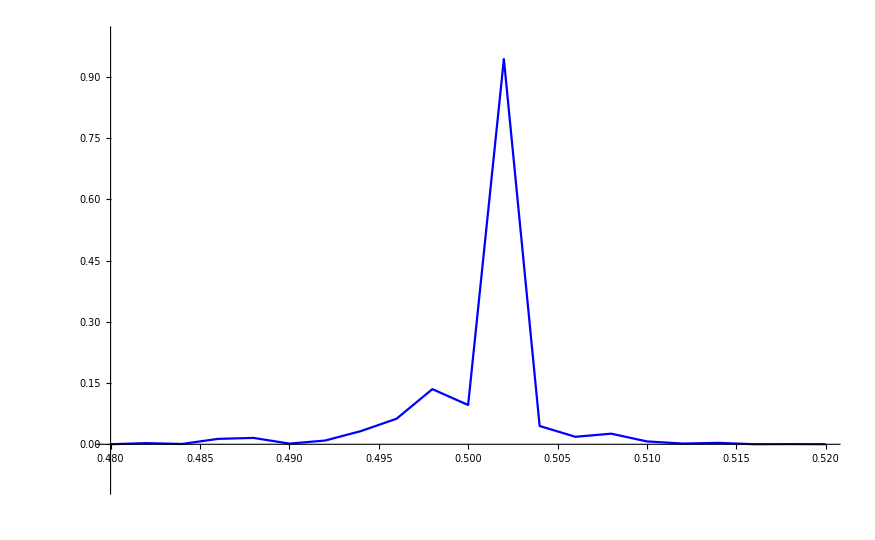

```mathematica
pdce=Plot[intdce[w],{w,0.48,0.52},PlotRange->{{0.48,0.52},{-0.1,1}},PlotStyle->Blue]
```

```mathematica
listdcelarge=Table[{1+0.002*z,noutdcelarge[z]},{z,240,260}]
```

{{1.48,8.06233×10^-6+0. ⅈ},{1.482,0.000114052+0. ⅈ},{1.484,0.0000486651+0. ⅈ},{1.486,0.00155266+0. ⅈ},{1.488,0.00123733+0. ⅈ},{1.49,0.0000413593+0. ⅈ},{1.492,0.00243653+0. ⅈ},{1.494,0.0131982+0. ⅈ},{1.496,0.0445638+0. ⅈ},{1.498,0.110988+0. ⅈ},{1.5,0.0406401+0. ⅈ},{1.502,4.00414+0. ⅈ},{1.504,0.0908839+0. ⅈ},{1.506,0.00478989+0. ⅈ},{1.508,0.00952492+0. ⅈ},{1.51,0.000429191+0. ⅈ},{1.512,0.000686761+0. ⅈ},{1.514,0.000136732+0. ⅈ},{1.516,0.0000118211+0. ⅈ},{1.518,0.0000130488+0. ⅈ},{1.52,6.93458×10^-6+0. ⅈ}}

```mathematica
intdcelarge=Interpolation[listdcelarge,InterpolationOrder->1]
```

InterpolatingFunction[{{1.48, 1.52}}, <>]

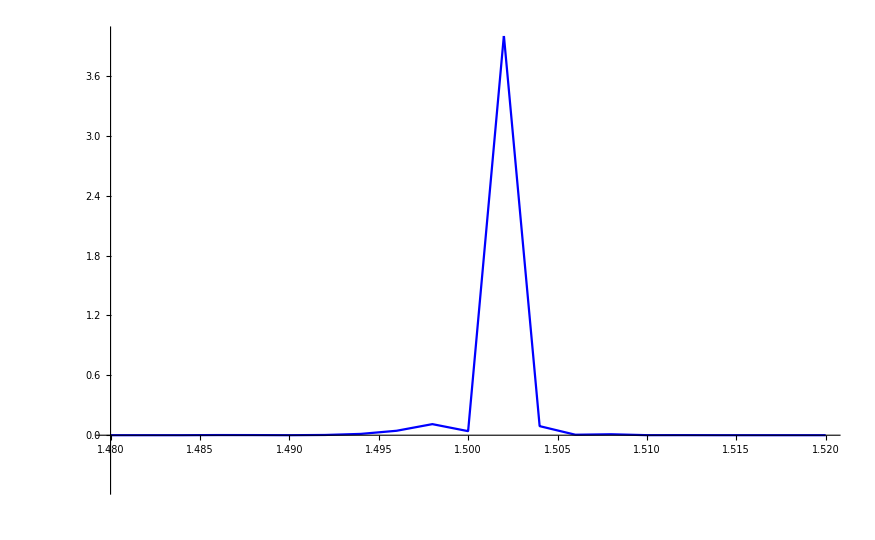

```mathematica
pdcelarge=Plot[intdcelarge[w],{w,1.48,1.52},PlotRange->{{1.48,1.52},{-0.5,4}},PlotStyle->{Blue}]
```

```mathematica
(* Radiation on left side *)
```

```mathematica
(* coefficients |C_nl|^2, |D_nl|^2, TR page 11 *)
```

```mathematica
ucc[m_]:=Conjugate[cc[[nomega+1,m]]] cc[[nomega+1,m]]      (* for omega_n = omega_k *)
```

```mathematica
vcc[m_]:=Conjugate[cc[[nomega,m]]] cc[[nomega,m]]                   (* for omega_n = Omega + omega_k *)
```

```mathematica
udd[m_]:=Conjugate[dd[[nomega+1,m]]] dd[[nomega+1,m]]
```

```mathematica
vdd[m_]:=Conjugate[dd[[nomega,m]]] dd[[nomega,m]]
```

```mathematica
nomega:=1    (* 1 sideband *)
```

```mathematica
Clear[q,r,s,t]
```

```mathematica
(* parameterize omega in [0.48, 0.52] in steps 0.002 => k = 240...260 in steps 1 *)
```

```mathematica
(* here I entered the lines for each k-value manually *)
```

```mathematica
nd:=500     (* # omega points in (0,Omega) *)
```

```mathematica
k:=260
```

```mathematica
ww[m_]:=k omega/nd +(nomega+1-m) omega
```

```mathematica
{q[k,1],q[k,2],q[k,3]}={ucc[1],ucc[2],ucc[3]}
```

{0.000277311+0. ⅈ,0.990284+0. ⅈ,0.000101234+0. ⅈ}

```mathematica
{r[k,1],r[k,2],r[k,3]}={udd[1],udd[2],udd[3]}
```

{0.000245885+0. ⅈ,0.0093961+0. ⅈ,0.000102286+0. ⅈ}

```mathematica
{s[k,1],s[k,2],s[k,3]}={vcc[1],vcc[2],vcc[3]}
```

{0.0748368+0. ⅈ,0.000277311+0. ⅈ,2.95645×10^-6+0. ⅈ}

```mathematica
{t[k,1],t[k,2],t[k,3]}={vdd[1],vdd[2],vdd[3]}
```

{0.924647+0. ⅈ,0.000245885+0. ⅈ,3.97813×10^-6+0. ⅈ}

```mathematica
(* here would be the "continue" comand for the loop *)
```

```mathematica
qdata:=Table[{k,m,Re[q[k,m]]},{k,240,260},{m,1,3}]
```

```mathematica
Export["q.dat",qdata]
```

q.dat

```mathematica
rdata:=Table[{k,m,Re[r[k,m]]},{k,240,260},{m,1,3}]
```

```mathematica
Export["r.dat",rdata]
```

r.dat

```mathematica
nin[ww_,t_]:= 1/(Exp[hbar Abs[ww]/(kb t)]-1)
```

```mathematica
www[k_,m_]:=k omega/nd +(nomega+1-m) omega
```

```mathematica
(* omega-region (0, Omega) *)
```

```mathematica
noutdceleft[k_]:=Sum[(q[k,m]+r[k,m]),{m,3,3}]
```

```mathematica
noutthermleft[k_,t_]:=Sum[(q[k,m]+r[k,m])nin[www[k,m],t],{m,1,3}]
```

```mathematica
noutbothleft[k_,t_]:=noutdceleft[k]+noutthermleft[k,t]
```

```mathematica
(* omega-region (Omega, 2 Omega) *)
```

```mathematica
noutdcelargeleft[k_]:=Sum[(s[k,m]+t[k,m]),{m,3,3}]
```

```mathematica
noutthermlargeleft[k_,t_]:=Sum[(s[k,m]+t[k,m])nin[www[k,m],t],{m,1,3}]
```

```mathematica
noutbothlargeleft[k_,t_]:=noutdcelargeleft[k]+noutthermlargeleft[k,t]
```

```mathematica
(* ell = 0.96*lambdaomega, nrepeat = 100 *)
```

```mathematica
listdceleft=Table[{0.002*z,noutdceleft[z]},{z,240,260}]
```

{{0.48,0.000173413+0. ⅈ},{0.482,0.00282841+0. ⅈ},{0.484,0.000759612+0. ⅈ},{0.486,0.0132611+0. ⅈ},{0.488,0.0155945+0. ⅈ},{0.49,0.00166736+0. ⅈ},{0.492,0.00914835+0. ⅈ},{0.494,0.0322711+0. ⅈ},{0.496,0.0626617+0. ⅈ},{0.498,0.135116+0. ⅈ},{0.5,0.0961773+0. ⅈ},{0.502,0.943454+0. ⅈ},{0.504,0.0448056+0. ⅈ},{0.506,0.0183358+0. ⅈ},{0.508,0.0259763+0. ⅈ},{0.51,0.00703254+0. ⅈ},{0.512,0.00179346+0. ⅈ},{0.514,0.00347578+0. ⅈ},{0.516,0.000190824+0. ⅈ},{0.518,0.000450385+0. ⅈ},{0.52,0.000203521+0. ⅈ}}

```mathematica
intdceleft=Interpolation[listdceleft,InterpolationOrder->1]
```

InterpolatingFunction[{{0.48, 0.52}}, <>]

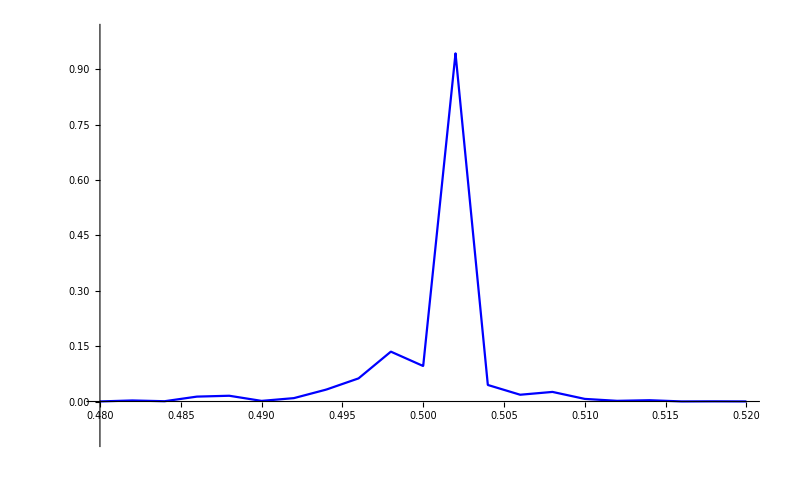

```mathematica
pdceleft=Plot[intdceleft[w],{w,0.48,0.52},PlotRange->{{0.48,0.52},{-0.1,1}},PlotStyle->Blue]
```

```mathematica
(* identical to radiation on right as expected *)
```

```mathematica
listtherm25=Table[{0.002*z,nouttherm[z,25 10^(-3)]},{z,240,260}]
```

{{0.48,3.56417×10^-8+0. ⅈ},{0.482,2.80481×10^-8+0. ⅈ},{0.484,2.59249×10^-8+0. ⅈ},{0.486,2.28447×10^-8+0. ⅈ},{0.488,2.52109×10^-8+0. ⅈ},{0.49,2.51587×10^-8+0. ⅈ},{0.492,2.14779×10^-8+0. ⅈ},{0.494,1.39002×10^-8+0. ⅈ},{0.496,1.57568×10^-8+0. ⅈ},{0.498,2.08054×10^-8+0. ⅈ},{0.5,1.87371×10^-8+0. ⅈ},{0.502,3.72771×10^-8+0. ⅈ},{0.504,1.57998×10^-8+0. ⅈ},{0.506,1.48732×10^-8+0. ⅈ},{0.508,1.11895×10^-8+0. ⅈ},{0.51,1.25888×10^-8+0. ⅈ},{0.512,1.13835×10^-8+0. ⅈ},{0.514,1.08124×10^-8+0. ⅈ},{0.516,9.96451×10^-9+0. ⅈ},{0.518,9.28324×10^-9+0. ⅈ},{0.52,8.64065×10^-9+0. ⅈ}}

```mathematica
inttherm25=Interpolation[listtherm25]
```

InterpolatingFunction[{{0.48, 0.52}}, <>]

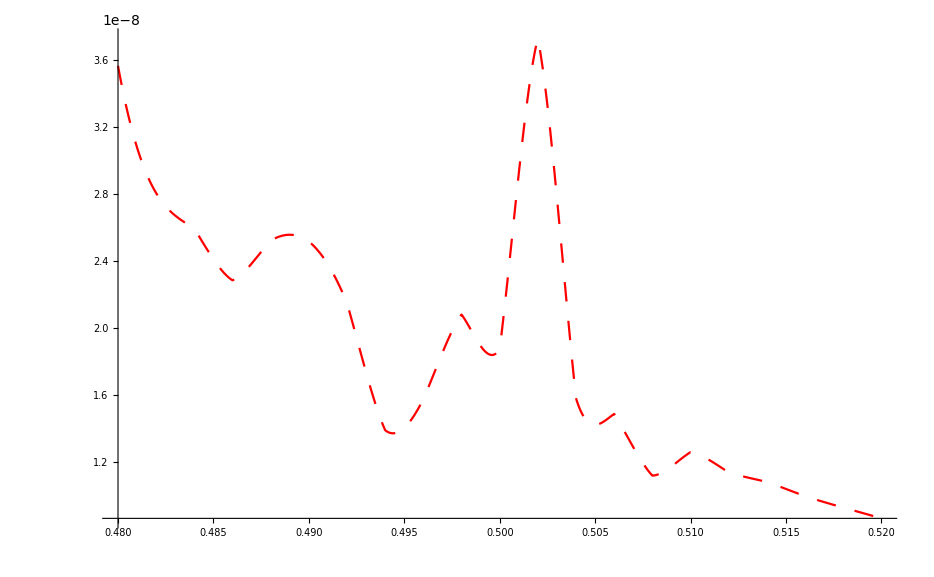

```mathematica
ptherm25=Plot[inttherm25[w],{w,0.48,0.52},PlotStyle->{Red,Dashing[Large]}]
```

```mathematica
(* negligible in comparison to DCE radiation *)
```